```mathematica
link=Install[LinkConnect["34463@192.168.217.129,35947@192.168.217.129",LinkProtocol->"TCPIP"]]
```

LinkObject[…]

```mathematica
handle=With[{mmin=50,mmax=1000,
ϵ=1./(16*1836.),ωeOΩe=1.2,Ωc=1.,
ηr={0.0002,0.001,0.001,0.0014,0.0013,0.0028,0.0037,0.0046,0.0046,0.0037,0.0027,0.0014,0.0014,0.001,0.001,0.0002},
vrr={0.2171,0.3636,0.5022,0.6404,0.7656,0.8059,0.8264,0.8513,0.8513,0.8264,0.7637,0.7656,0.6404,0.5022,0.3445,0.2059},
vrd={0.9844,0.9398,0.8103,0.7030,0.5778,0.4012,0.2355,0.0785,-0.0785,-0.2355,-0.3802,-0.5778,-0.7030,-0.8103,-0.8906,-0.9329},
vthj ={0.326,0.2795,0.2795,0.2562,0.2562,0.2329,0.2329,0.1863,0.1863,0.2329,0.2329,0.2562,0.2562,0.2795,0.2795,0.326}*0.3
},
Module[{
ηs={0.864,0.0232,0.006,0.0606,0.0142,Sequence@@ηr,1.},
θs={0.032,0.19,0.1,0.06,0.21,Sequence@@vthj,0.1*√(1/ϵ)},
Ωcs,ωps2,θ1s,θ2s,vrs,vds,c
}, c=ωeOΩe/√ϵ;
Ωcs={16,16,4,1,1,Sequence@@ConstantArray[1,Length[ηr]],-1/ϵ}Ωc//N;
ωps2=c^2 ηs{16,16,4,1,1,Sequence@@ConstantArray[1,Length[ηr]],1/ϵ}Ωc^2//N;
θ1s=θs;
θ2s=θs;
vrs={0,0,0,0,0,Sequence@@vrr,0}//N;
vds={0,0,0,0,0,Sequence@@vrd,0}//N;
(*distribution functions*)
dist=Thread[wstpDRingDistribution[Ωcs,Sqrt[ωps2],θs,θs,vds,vrs]];
wstpDCreateDispersionObject[c,dist]]];
```

```mathematica
handle//wstpDDescription
wstpDSetMinimumCyclotronOrder[handle,200]
```

N4Disp10DispersionE[c->205.673, jmin->5, jmax->2000, vdfs->{
	N4Disp17MaxwellianRingVDFE[Oc->16, op->(764.706,0), th1->0.032, th2->0.032, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->16, op->(125.309,0), th1->0.19, th2->0.19, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->4, op->(31.8627,0), th1->0.1, th2->0.1, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(50.6307,0), th1->0.06, th2->0.06, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(24.5088,0), th1->0.21, th2->0.21, vd->0, vr->0],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(2.90866,0), th1->0.0978, th2->0.0978, vd->0.9844, vr->0.2171],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->0.9398, vr->0.3636],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->0.8103, vr->0.5022],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->0.703, vr->0.6404],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.41565,0), th1->0.07686, th2->0.07686, vd->0.5778, vr->0.7656],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(10.8832,0), th1->0.06987, th2->0.06987, vd->0.4012, vr->0.8059],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(12.5106,0), th1->0.06987, th2->0.06987, vd->0.2355, vr->0.8264],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(13.9494,0), th1->0.05589, th2->0.05589, vd->0.0785, vr->0.8513],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(13.9494,0), th1->0.05589, th2->0.05589, vd->-0.0785, vr->0.8513],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(12.5106,0), th1->0.06987, th2->0.06987, vd->-0.2355, vr->0.8264],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(10.6871,0), th1->0.06987, th2->0.06987, vd->-0.3802, vr->0.7637],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->-0.5778, vr->0.7656],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(7.69558,0), th1->0.07686, th2->0.07686, vd->-0.703, vr->0.6404],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->-0.8103, vr->0.5022],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(6.50396,0), th1->0.08385, th2->0.08385, vd->-0.8906, vr->0.3445],
	N4Disp17MaxwellianRingVDFE[Oc->1, op->(2.90866,0), th1->0.0978, th2->0.0978, vd->-0.9329, vr->0.2059],
	N4Disp17MaxwellianRingVDFE[Oc->-29376, op->(35251.2,0), th1->17.1394, th2->17.1394, vd->0, vr->0]
}]

{200,2000}

```mathematica
With[{handle=handle,k1=0.55,k0=6.,ω0=2.9+0.1I},
"ω"/.wstpDFindRoot[handle,k1,k0,ω0 (1+0.01 I {0,1,2}),MaxIterations->10,"UpdateMinimumCyclotronOrderFromPreviousIteration"->False,"ReturnDispersionMatrix"->False]]
```

2.68013+0.0211183 ⅈ

```mathematica
check=With[{k1=0.6,k0=6.0},wstpDFindRoot[handle,k1,k0,Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
```

{2.74301-0.0216825 ⅈ,2.73009-0.0215456 ⅈ,2.71716-0.0208854 ⅈ,2.70421-0.0194608 ⅈ,2.69132-0.0168145 ⅈ,2.67872-0.0119406 ⅈ,2.66804-0.00232774 ⅈ,2.66894+0.0142214 ⅈ,2.70575+0.032872 ⅈ,2.73886+0.0632278 ⅈ,2.77622+0.0789947 ⅈ}

{2.74301-0.0216825 ⅈ,2.73009-0.0215456 ⅈ,2.71716-0.0208854 ⅈ,2.70421-0.0194608 ⅈ,2.69132-0.0168145 ⅈ,2.67872-0.0119406 ⅈ,2.66804-0.00232774 ⅈ,2.66894+0.0142214 ⅈ,2.70575+0.032872 ⅈ,2.73886+0.0632278 ⅈ,2.77622+0.0789947 ⅈ,2.81725+0.0900338 ⅈ,2.85968+0.0961142 ⅈ,2.90373+0.0992069 ⅈ,2.94752+0.0981142 ⅈ,2.99506+0.092973 ⅈ,3.04272+0.089239 ⅈ,3.0888+0.0803256 ⅈ,3.1397+0.070778 ⅈ,3.18517+0.0618553 ⅈ,3.22984+0.0422141 ⅈ,3.28773+0.0310614 ⅈ,3.3241+0.0210747 ⅈ,3.34797+0.0042113 ⅈ,3.359-0.0128022 ⅈ,3.36522-0.0279163 ⅈ,3.373-0.043736 ⅈ,3.39059-0.0581491 ⅈ,3.40845-0.053572 ⅈ,3.41257-0.0502881 ⅈ,3.41434-0.0518841 ⅈ}

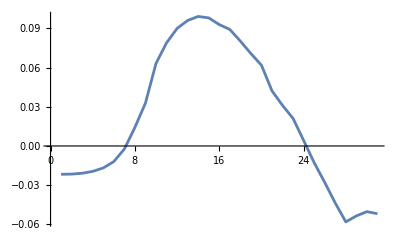

```mathematica
toleft=With[{k1=Range[0.6,0.4,-0.02]},wstpDFindRoot[handle,k1,ConstantArray[6.0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
toright=With[{k1=Range[0.62,1.0,0.02]},wstpDFindRoot[handle,k1,ConstantArray[6.0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100]];
l=Reverse[toleft[[2,2]]]
total=Join[l,toright[[2,2]]]
ListLinePlot[Im[total]]
```

```mathematica
result={};
With[{k1=Range[0.4,0.6,0.05]},

Do[sol=wstpDFindRoot[handle,k1,ConstantArray[k0,Length[k1]],Complex[2.9,0.05] (1+0.0001 I {0,1,2}),MaxIterations->100];
result=Append[result,sol[[2]]],
{k0,5.9,6.1,0.1}]];
result
```

{ω→{2.74304-0.0218599 ⅈ,2.26814+0.0318086 ⅈ,2.35848+0.0264414 ⅈ,2.43738-0.00726941 ⅈ,2.44199-0.0361933 ⅈ},ω→{2.74301-0.0216824 ⅈ,2.27842+0.0312775 ⅈ,2.36686+0.0239275 ⅈ,2.44328-0.00955456 ⅈ,2.44237-0.0384055 ⅈ},ω→{2.74297-0.0216716 ⅈ,2.28774+0.0307842 ⅈ,2.37471+0.0212495 ⅈ,2.44824-0.0114764 ⅈ,2.44261-0.0403902 ⅈ}}